```mathematica
SetDirectory[DirectoryName[ToFileName["FileName"/.NotebookInformation[SelectedNotebook[]]]]]
```

/home/tbjc1magic/Geant4/tbjc11

```mathematica
datalist=Import["steppoint.dat"];
```

```mathematica
plotlist=Transpose[{Transpose[datalist][[3]]/10,Transpose[datalist][[5]]}];
```

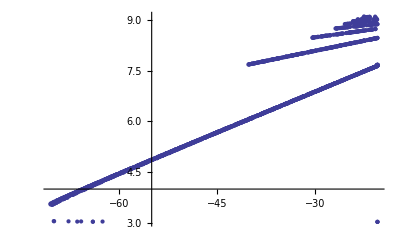

```mathematica
ListPlot[plotlist,PlotRange->{{-50,-55},{4,6}}]
```